## Solution CP7: Systems of ODEs

This exercise demonstrates how Mathematica can be used to solve linear second-order ODEs and systems of ODEs

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Linear second-order ODEs

Entering a second-order ODE is very similar to what we have seen in CP3. We use the command D[] to calculate the first and second derivatives, and the command DSolveValue[] to solve the resulting differential equation. For a second-order ODE z''(t)=a·z'(t)+b·z(t) we need to define initial values for z(0)  and z'(0).
The commands Plot[] and ParametricPlot[] are used to create time plots and phase plots of a solution, respectively.

### Exercise 7-1

Calculate and plot the solution of the following second-order differential equations for initial values z(0)=2 and dz/dt(0)=1:

(a)  (ⅆ^2 z)/(ⅆ t^2)=1/2·ⅆz/ⅆt+3/16·z

z''[t]==(3 z[t])/16+z'[t]/2

{z[0]==2,z'[0]==1}

1/2 ⅇ^(-t/4) (1+3 ⅇ^t)

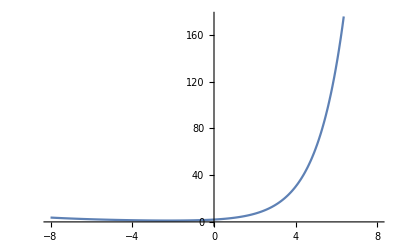

```mathematica
DV=D[z[t],{t,2}]==(1/2)*D[z[t],t]+(3/16)*z[t]
init={z[0]==2,z'[0]==1}
sol=DSolveValue[{DV,init},z[t],t]
Plot[sol,{t,-8,8}]
```

(b)  (ⅆ^2 z)/(ⅆ t^2)=-2·ⅆz/ⅆt-2·z

z''[t]==-2 z[t]-2 z'[t]

ⅇ^-t (2 Cos[t]+3 Sin[t])

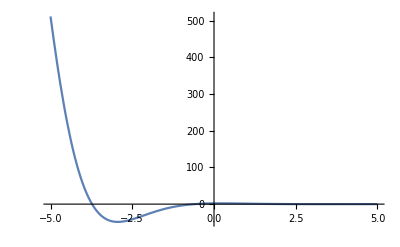

```mathematica
DV=D[z[t],{t,2}]==-2*D[z[t],t]-2*z[t]
init={z[0]==2,z'[0]==1};
sol=DSolveValue[{DV,init},z[t],t]
Plot[sol,{t,-5,5},PlotRange->All]
```

### Exercise 7-2

Calculate and plot the solution of the following linear systems of differential equations for initial values x(0)=2 and y(0)=0:

(a)  ⅆx/ⅆt=1/4 x+1/2 y, ⅆy/ⅆt=1/2 x+1/4 y

```mathematica
eqX=D[x[t],t]==(1/4)*x[t]+(1/2)*y[t]
eqY=D[y[t],t]==(1/2)*x[t]+(1/4)*y[t]
sysODE={eqX,eqY};
init={x[0]==2,y[0]==0};
sol=DSolveValue[{sysODE,init},{x[t],y[t]},t]
```

x'[t]==x[t]/4+y[t]/2

y'[t]==x[t]/2+y[t]/4

{ⅇ^(-t/4) (1+ⅇ^t),ⅇ^(-t/4) (-1+ⅇ^t)}

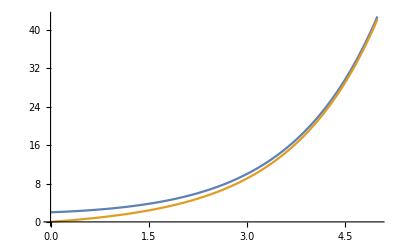

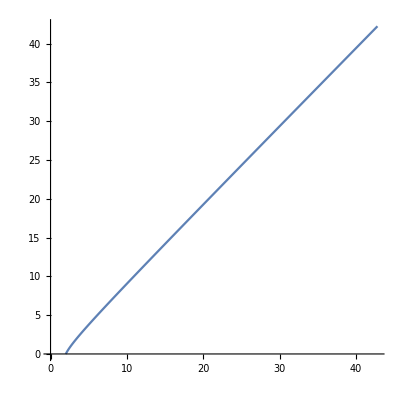

```mathematica
Plot[sol,{t,0,5},PlotRange->Full]
ParametricPlot[sol,{t,0,5}]
```

(b)  ⅆx/ⅆt=-x-y, ⅆy/ⅆt=x-y

```mathematica
eqX=D[x[t],t]==-x[t]-y[t]
eqY=D[y[t],t]==x[t]-y[t]
sysODE={eqX,eqY};
init={x[0]==2,y[0]==0};
sol=DSolveValue[{sysODE,init},{x[t],y[t]},t]
```

x'[t]==-x[t]-y[t]

y'[t]==x[t]-y[t]

{2 ⅇ^-t Cos[t],2 ⅇ^-t Sin[t]}

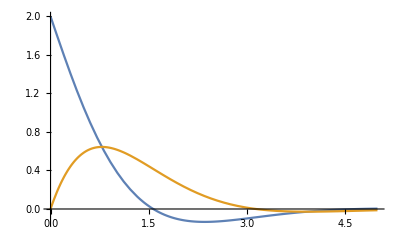

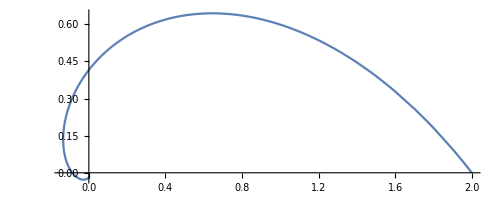

```mathematica
Plot[sol,{t,0,5},PlotRange->Full]
ParametricPlot[sol,{t,0,5}]
```

### Exercise 7-3

Hooke’s Law can be described by the second-order differential equation:  m·(ⅆ^2 x)/(ⅆ t^2)=-c·ⅆx/ⅆt-k·x
Consider this equation for specific conditions m=1 and k=4 and the following three scenarios:
(i) c=0 (no friction)
(ii) c=2 (low friction)
(iii) c=5 (heavy friction)

(a) Solve the equation for each scenario and initial conditions x(0)=2  and dx/dt(0)=0

```mathematica
DV=m*D[x[t],{t,2}]==-c*D[x[t],t]+-k*x[t]
init={x[0]==2,x'[0]==0}
sol=DSolveValue[{DV,init},x[t],t]
```

m x''[t]==-k x[t]-c x'[t]

{x[0]==2,x'[0]==0}

1/(√(c^2-4 k m))(-c ⅇ^(1/2 (-c/m-(√(c^2-4 k m))/m) t)+c ⅇ^(1/2 (-c/m+(√(c^2-4 k m))/m) t)+ⅇ^(1/2 (-c/m-(√(c^2-4 k m))/m) t) √(c^2-4 k m)+ⅇ^(1/2 (-c/m+(√(c^2-4 k m))/m) t) √(c^2-4 k m))

```mathematica
scen1={m->1,k->4,c->0};
scen2={m->1,k->4,c->2};
scen3={m->1,k->4,c->5};
```

```mathematica
sol1=ExpToTrig[sol/.scen1]
sol2=Simplify[ExpToTrig[sol/.scen2]]
sol3=Simplify[sol/.scen3]
```

2 Cos[2 t]

2/3 (3 Cos[√3 t]+√3 Sin[√3 t]) (Cosh[t]-Sinh[t])

2/3 ⅇ^(-4 t) (-1+4 ⅇ^(3 t))

(b) Plot all three scenarios in one graph. What can you conclude?

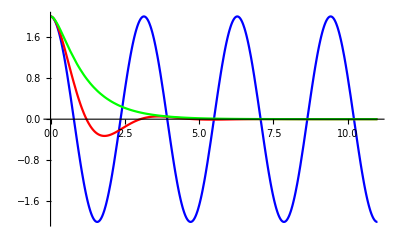

```mathematica
Plot[{sol1,sol2,sol3},{t,0,11},PlotRange->All,PlotStyle->{Blue,Red,Green}]
```

Without friction, the system oscillates between initial values +2 and -2. The heavier the friction, the faster the movement dies out.

### Exercise 7-4

In this exercise, we compare a system of differential equations to a system of recurrence (difference) equations
differentail equations:  ⅆx/ⅆt=-0.1x+y, ⅆy/ⅆt=0.2x-0.2y
Recurrence equations:  x(t+1)=-0.1x(t)+y(t), y(t+1)=0.2x(t)-0.2y(t)

(a) Calculate a general solution for both systems with initial values x(0)=y(0)=1

```mathematica
eqX=D[x[t],t]==-0.1*x[t]+y[t]
eqY=D[y[t],t]==0.2*x[t]-0.2*y[t]
sysODE={eqX,eqY};
init={x[0]==1,y[0]==1};
sol=DSolveValue[{sysODE,init},{x[t],y[t]},t]
```

x'[t]==-0.1 x[t]+y[t]

y'[t]==0.2 x[t]-0.2 y[t]

{1.66667 ⅇ^(-0.6 t) (-0.4+1. ⅇ^(0.9 t)),0.666667 ⅇ^(-0.6 t) (0.5+1. ⅇ^(0.9 t))}

```mathematica
eqX1=x[t+1]==-0.1*x[t]+y[t]
eqY1=y[t+1]==0.2*x[t]-0.2*y[t]
sys1={eqX1,eqY1};
init1={x[0]==1,y[0]==1};
{sol1,sol2}=Simplify[RSolveValue[{sys1,init1},{x[t],y[t]},t]]
```

x[1+t]==-0.1 x[t]+y[t]

y[1+t]==0.2 x[t]-0.2 y[t]

{(-0.666667 (-1.35108×10^16)^t+1.66667 (6.7554×10^15)^t) ⅇ^(-37.6531 t),(0.333333 (-1.35108×10^16)^t+0.666667 (6.7554×10^15)^t) ⅇ^(-37.6531 t)}

(b)  Plot the solutions for both systems, and describe what happens for t -> ∞. Can you explain the different behaviour of the two types of systems?

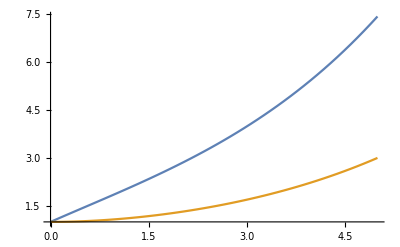

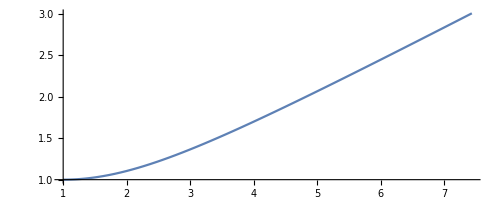

```mathematica
Plot[sol,{t,0,5},PlotRange->Full]
ParametricPlot[sol,{t,0,5}]
```

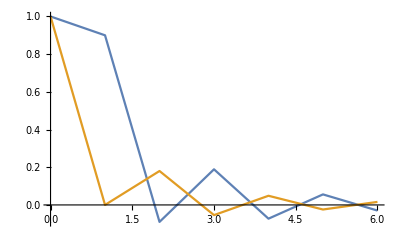

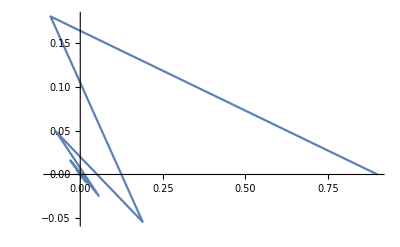

```mathematica
DiscretePlot[{sol1,sol2},{t,0,6},Joined->True,Filling->None]
pts=RecurrenceTable[{eqX1,eqY1,init1},{x[t],y[t]},{t,1,10}];
ListLinePlot[pts,PlotRange->All]
```

The continuous system diverged to infinity, because the positve exponential diverges to infinity over time. In the discrete system both terms converge to zero, hence the solution will converghe to zero over time.